# Stepper motor acceleration

## Determining angular velocity ω by delay τ

The angular velocity of a stepper motor is defined by the angle per step α and the time delay τ between steps.

The time delay is generally given by

```mathematica
delay[ConstDelay_,DelayFactor_]:=Function[{n},ConstDelay+n DelayFactor]
```

```mathematica
ω->α/τ
%/.τ->delay[c,d][n]
```

ω→α/τ

ω→α/(c+d n)

## For a constant angular acceleration ⅆω/ⅆt, we want ω to increase linearly.

```mathematica
ω->α/τ
%/.τ->delay[c,d][n]
Ω t==ω/.%
Last[Solve[%,n]]
```

ω→α/τ

ω→α/(c+d n)

t Ω==α/(c+d n)

{n→(α-c t Ω)/(d t Ω)}

## Heuristic for constant acceleration

delay→dividend/divisor

ω→α/delay

ω→(divisor α)/dividend

ω→{α/2000,α/1000,(3 α)/2000,α/500,α/400,(3 α)/1000,(7 α)/2000,α/250,(9 α)/2000,α/200,(11 α)/2000,(3 α)/500,(13 α)/2000,(7 α)/1000,(3 α)/400,α/125,(17 α)/2000,(9 α)/1000,(19 α)/2000,α/100,(21 α)/2000,(11 α)/1000,(23 α)/2000,(3 α)/250,α/80,(13 α)/1000,(27 α)/2000,(7 α)/500,(29 α)/2000,(3 α)/200,(31 α)/2000,(2 α)/125,(33 α)/2000,(17 α)/1000,(7 α)/400,(9 α)/500,(37 α)/2000,(19 α)/1000,(39 α)/2000,α/50,(41 α)/2000,(21 α)/1000,(43 α)/2000,(11 α)/500,(9 α)/400,(23 α)/1000,(47 α)/2000,(3 α)/125,(49 α)/2000,α/40,(51 α)/2000,(13 α)/500,(53 α)/2000,(27 α)/1000,(11 α)/400,(7 α)/250,(57 α)/2000,(29 α)/1000,(59 α)/2000,(3 α)/100,(61 α)/2000,(31 α)/1000,(63 α)/2000,(4 α)/125,(13 α)/400,(33 α)/1000,(67 α)/2000,(17 α)/500,(69 α)/2000,(7 α)/200,(71 α)/2000,(9 α)/250,(73 α)/2000,(37 α)/1000,(3 α)/80,(19 α)/500,(77 α)/2000,(39 α)/1000,(79 α)/2000,α/25,(81 α)/2000,(41 α)/1000,(83 α)/2000,(21 α)/500,(17 α)/400,(43 α)/1000,(87 α)/2000,(11 α)/250,(89 α)/2000,(9 α)/200,(91 α)/2000,(23 α)/500,(93 α)/2000,(47 α)/1000,(19 α)/400,(6 α)/125,(97 α)/2000,(49 α)/1000,(99 α)/2000,α/20}

{0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016,0.0165,0.017,0.0175,0.018,0.0185,0.019,0.0195,0.02,0.0205,0.021,0.0215,0.022,0.0225,0.023,0.0235,0.024,0.0245,0.025,0.0255,0.026,0.0265,0.027,0.0275,0.028,0.0285,0.029,0.0295,0.03,0.0305,0.031,0.0315,0.032,0.0325,0.033,0.0335,0.034,0.0345,0.035,0.0355,0.036,0.0365,0.037,0.0375,0.038,0.0385,0.039,0.0395,0.04,0.0405,0.041,0.0415,0.042,0.0425,0.043,0.0435,0.044,0.0445,0.045,0.0455,0.046,0.0465,0.047,0.0475,0.048,0.0485,0.049,0.0495,0.05}

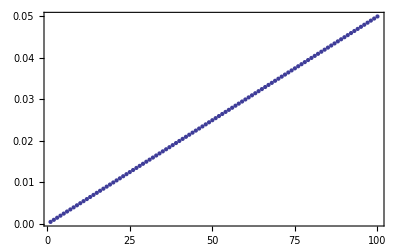

```mathematica
delay->dividend/divisor
ω->α/delay
%/.%%
%//.{dividend->2000,divisor->Range[dividend/ωmax],ωmax->20}
N[ω/.%/.α->1]
ListPlot[%,Frame->True]
```